# Calculation of eikonal corrections at KE = 210 MeV

9/11/13

## Define constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.210(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

```mathematica
(1/4/ℏc)^2/6
```

0.26752

```mathematica
Sqrt[6 B]*ℏc
```

1.67444

```mathematica
1.25*4^(1/3)
```

1.98425

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
pp210a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210a.csv"];
pp210b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210b.csv"];
```

```mathematica
(*pp210a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp210a.csv"];
pp210b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp210b.csv"];*)
```

```mathematica
pp210a=Transpose[{pp210a[[All,1]],pp210a[[All,2]]+I*pp210a[[All,3]]}];
pp210b=Transpose[{pp210b[[All,1]],pp210b[[All,2]]+I*pp210b[[All,3]]}];
```

```mathematica
θpp210=Transpose[{pp210a[[All,1]],(pp210a[[All,2]]+pp210b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp210=θtoq/@θpp210;
```

```mathematica
pn210a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn210a.csv"];
pn210b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn210b.csv"];
```

```mathematica
(*pn210a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn210a.csv"];
pn210b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn210b.csv"];*)
```

```mathematica
pn210a=Transpose[{pn210a[[All,1]],pn210a[[All,2]]+I*pn210a[[All,3]]}];
pn210b=Transpose[{pn210b[[All,1]],pn210b[[All,2]]+I*pn210b[[All,3]]}];
```

```mathematica
θpn210=Transpose[{pn210a[[All,1]],(pn210a[[All,2]]+pn210b[[All,2]])/2}];
```

```mathematica
pn210=θtoq/@θpn210;
```

```mathematica
NN210=(pp210+pn210)/2;
```

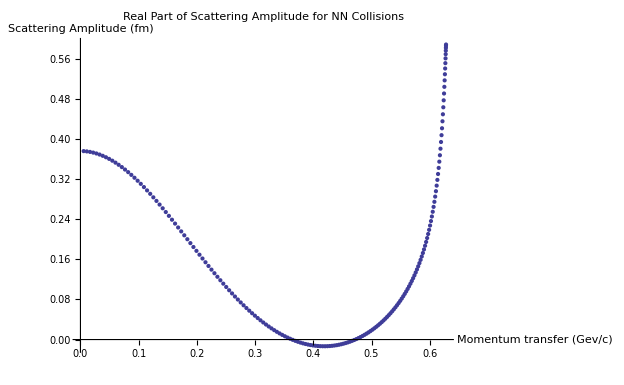

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Re[NN210[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

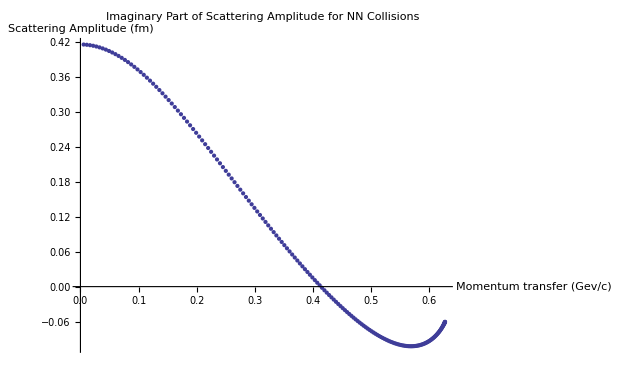

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Im[NN210[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

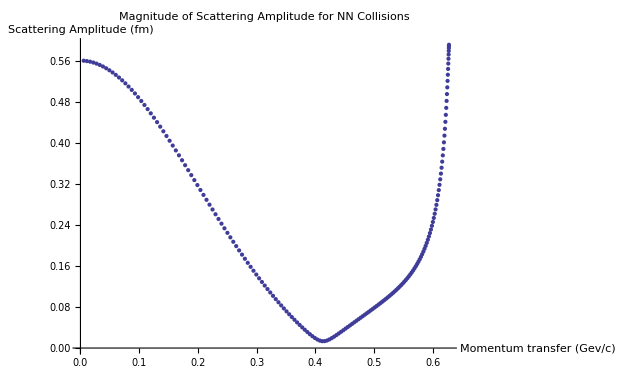

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Abs[NN210[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

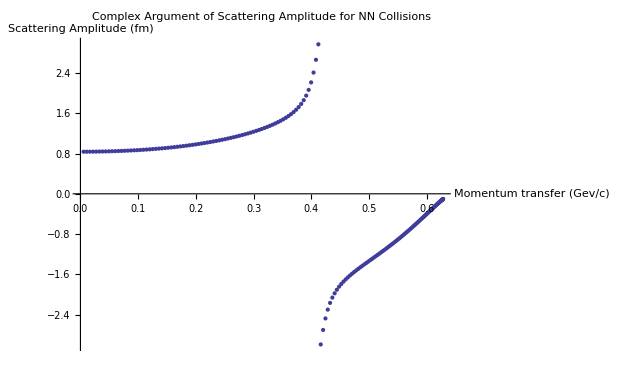

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Arg[NN210[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{σ→4.4436,βre→14.4438}

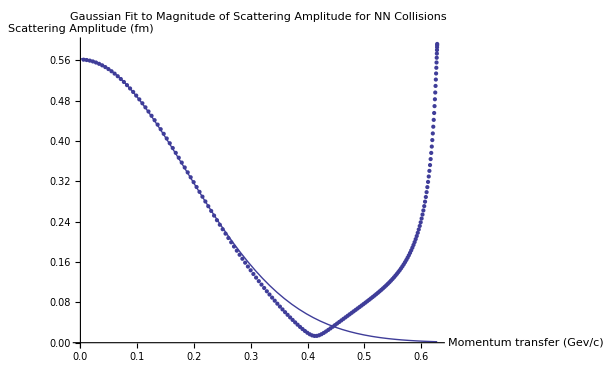

```mathematica
Npts=50;
FindFit[Transpose[{NN210[[1;;Npts,1]],Abs[NN210[[1;;Npts,2]]]}],κ/ℏc σ/(4 Pi) Exp[-βre q^2],{σ,βre},q]
Show[Plot[κ/ℏc σ/(4 Pi) Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN210[[All,1]],Abs[NN210[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->All]
```

```mathematica
(4.18-I 2.70) Exp[-(16-I 5.66) q^2]/(2 I κ)
```

{ρ→0.916394,βim→-3.97743}

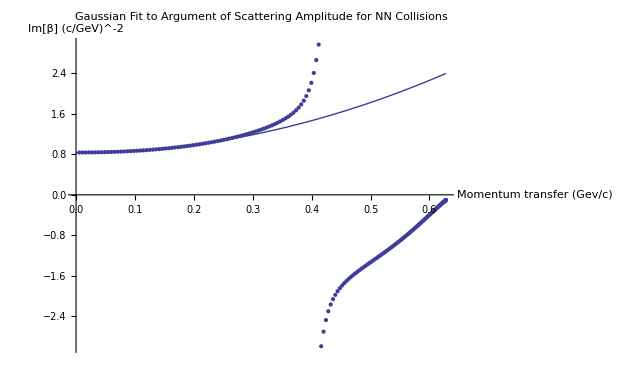

```mathematica
FindFit[Transpose[{NN210[[1;;Npts,1]],Arg[NN210[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN210[[All,1]],Arg[NN210[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Im[β] (c/GeV)^-2"}]
```

Fitted parameters:

```mathematica
σ=4.443604017453662;
ρ=0.9163935163116479;
β=14.4437913447594-3.977429080580476 I;
```

## Glauber

```mathematica
σ=4.4;
ρ=-0.3;
β=2.72;
```

```mathematica
σ1=σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

1.65299+0.495898 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber approximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

143.161

## Add in First Order Correction

```mathematica
Γ[b_]:=σ1 Exp[-b^2/(4 β)]
```

```mathematica
Γ[0]
```

1.65299+0.495898 ⅈ

```mathematica
U[q_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-Γ[b]],{b,0,Infinity}]
```

```mathematica
U[0]
```

61.3622-55.5937 ⅈ

Wallace parameterizes it as a gaussian in q, so we should check the validity of that assertion:

```mathematica
Quiet[Table[{q,Abs[U[Sqrt[q]]/(-I 4 Pi β σ1)]},{q,0.001,1.001,.1}]]
```

{{0.001,1.40046},{0.101,1.11644},{0.201,0.897004},{0.301,0.72749},{0.401,0.596527},{0.501,0.495274},{0.601,0.41684},{0.701,0.355852},{0.801,0.308127},{0.901,0.270432},{1.001,0.240296}}

```mathematica
interp1=Interpolation[{{0.001,1.400464834010183},{0.101,1.1164369310416329},{0.201,0.8970035785026615},{0.30100000000000005,0.7274902936255093},{0.401,0.5965268434657213},{0.501,0.49527368049525367},{0.6010000000000001,0.41684033756496586},{0.7010000000000001,0.3558519078093624},{0.801,0.30812656510772096},{0.901,0.27043220587575},{1.001,0.24029634426290844}}];
```

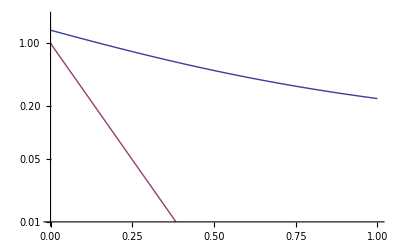

```mathematica
Quiet[LogPlot[{interp1[t],Exp[-B t]},{t,0,1},PlotRange->{.01,2}]]
```

The magnitude seems to be well approximated by a gaussian.

```mathematica
Quiet[Table[{q,Arg[U[Sqrt[q]/(-I 4 Pi β σ1)]]},{q,0.001,1.001,.1}]]
```

{{0.001,-2.37059},{0.101,-2.07543},{0.201,-1.89454},{0.301,-1.88829},{0.401,-2.02714},{0.501,-2.15945},{0.601,-2.22303},{0.701,-2.25229},{0.801,-2.27953},{0.901,-2.31659},{1.001,-2.36235}}

```mathematica
interp2=Interpolation[{{0.001,-2.3705875075728087},{0.101,-2.0754306673181375},{0.201,-1.8945409495838688},{0.30100000000000005,-1.888292098608192},{0.401,-2.027144824323856},{0.501,-2.1594459700001813},{0.6010000000000001,-2.223030697780126},{0.7010000000000001,-2.2522913102638236},{0.801,-2.279532063043649},{0.901,-2.3165913862754377},{1.001,-2.362351936150366}}];
```

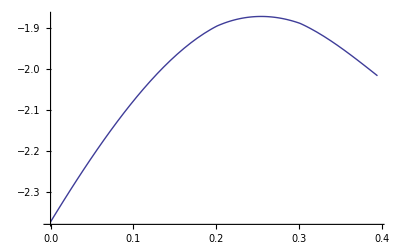

```mathematica
Quiet[Plot[interp2[t],{t,0,(2 κ)^2}]]
```

```mathematica
Quiet[U[.1]]
```

-51.8272-53.4335 ⅈ

```mathematica
γ=100*Quiet[(Log[U[0]]-Log[U[0.1]])]
```

13.8312-3.29766 ⅈ

```mathematica
Z=U[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

1.1024-0.06768 ⅈ

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1:=γ*β/(γ+β)(*(c/GeV)^2*)
αnL[n_,L_]:=If[n==1,(2*(γ+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ+B)^-1+(γ1+B)^-1+L*(β+B)^-1)^-1,If[n==3,(2*(γ1+B)^-1+L*(β+B)^-1)^-1]]]
an[n_]:=If[n==1,(γ+B)^-2,If[n==2,-2*σ1*(γ1/γ)*(γ+B)^-1*(γ1+B)^-1,If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-2]]]
bn[n_]:=If[n==1,(γ+B)^-3,If[n==2,-σ1*(γ1/γ)*(γ1+B)^-1*(γ+B)^-1*((1-B*γ1/(β*(B+γ1)))/(γ+B)+(1-γ1/β)/(γ1+B)),If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-3*(1-B*γ1/(β*(B+γ1)))*(1-γ1/β)]]]
γ2:=γ*β/(β+2*γ)(*(c/GeV)^2*)
βnL[n_,L_]:=If[n==1,((γ/2+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ2/2+B)^-1+L*(β+B)^-1)^-1]]
cn[n_]:=If[n==1,(γ-2*B)*(γ+2*B)^-2,If[n==2,-σ1(γ2/γ1)*(γ2+2*B)^-1*(1-2*γ2/γ+2*(γ2)^2/(γ*(γ2+2*B)))]]
dn[n_]:=If[n==1,γ*(γ+2*B)^-3,If[n==2,
-σ1*(γ)^-2*(γ2/(γ2+2*B))^3]]
```

```mathematica
FO1[q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO*(β*σ1*Z)^2/(2*(2*Pi*(B+β))^(1/2))*Sum[Binomial[A-2,L]*(-σ1*β/(B+β))^L*Sum[αnL[n,L]*(an[n]-4*αnL[n,L]*bn[n]*(1-αnL[n,L]q^2))*Exp[-αnL[n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1[q_(*c/GeV*)]:=A*Fcm[q]*ηD*(β*σ1*Z)^2/(2*γ*Sqrt[2*Pi*γ])*Sum[Binomial[A-1,L]*(-σ1*β/(B+β))^L*Sum[βnL[n,L]*(cn[n]-4*βnL[n,L]*dn[n]*(1-βnL[n,L]*q^2))*Exp[-βnL[n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

```mathematica
Im[FO1[0]+FD1[0]]/Im[F0[0]+FO1[0]+FD1[0]]
```

0.002791

The first order correction is about 0.3% at 210 MeV.

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]+F0[0]]
```

166.651

0.466426

167.118

```mathematica
FO1[0]
```

-0.012968+0.037064 ⅈ

```mathematica
FD1[0]
```

0.0130009-0.0274403 ⅈ